```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\code\mathematica\IT3sem\practice

```mathematica
data=Import["problem.txt", "Table"];
```

```mathematica
npts=data[[1,1]]
```

124

```mathematica
ncells=data[[npts+2,1]]
```

206

```mathematica
pts=data[[2;;npts+1]];
```

```mathematica
cells=data[[npts+4;;npts+4+411;;2]]/.i_Integer:>data[[i+1]] ;
```

```mathematica
img=Graphics[{White,EdgeForm[Thin],Polygon[cells]}]
```

-Graphics-

```mathematica
xslab=Sort@Table[pts[[i,1]],{i,npts}];
```

```mathematica
(*testdata=data[[4+npts+2ncells;;]];*)
```

```mathematica
testdata=Import["testdata2.txt","Table"][[2;;]];
```

```mathematica
(*testdata1=Cases[Table[{RandomReal[{-1.4,1.4}],RandomReal[{-0.9,0.9}]},{i,1,12000}],p_/;(p[[1]])^2/2.25+(p[[2]])^2<=1+$MachineEpsilon];*)
```

```mathematica
(*Export["testdata.txt",{Length@testdata1}~Join~testdata1, "Table"]*)
```

```mathematica
time=Table[{0},{20}]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
time[[1]]=AbsoluteTiming[slabs=Cases[Table[{xslab[[i]],xslab[[i+1]]},{i,npts-1}],x_/;x[[2]]-x[[1]]>0];][[1]]
```

0.0002283

```mathematica
time[[2]]=AbsoluteTiming[setxslab=slabs[[All,1]]~Join~{slabs[[-1,-1]]};][[1]]
```

0.0000204

```mathematica
search[arr_,pt_]:=Module[{low=1,high=Length@arr,mid},While[low<=high,mid=Floor[low+(high-low)/2];
If[Abs[arr[[mid]]-pt]<10^-10,Return[mid],If[pt<arr[[mid]],high=mid-1,low=mid+1]]];
Return[low-1]]
```

```mathematica
xRange[fig_]:=Return[{Min[fig[[All,1]]],Max[fig[[All,1]]]}]
```

```mathematica
MyMin[cell_,slab_]:= Module[{pair= {},y={}},For[i=1,i<=Length@cell,++i,
If[Min[cell[[i,1]],cell[[Mod[i,Length@cell]+1,1]]]<slab[[1]]&&(Max[cell[[i,1]],cell[[Mod[i,Length@cell]+1,1]]]>slab[[2]]||Abs[Max[cell[[i,1]],cell[[Mod[i,Length@cell]+1,1]]]-slab[[2]]]<10^-10)||Max[cell[[i,1]],cell[[Mod[i,Length@cell]+1,1]]]>slab[[2]]&&(Min[cell[[i,1]],cell[[Mod[i,Length@cell]+1,1]]]<slab[[1]]||Abs[Min[cell[[i,1]],cell[[Mod[i,Length@cell]+1,1]]]-slab[[1]]]<10^-10) ||
(Abs[Min[cell[[i,1]],cell[[Mod[i,Length@cell]+1,1]]]-slab[[1]]]<10^-10 &&Abs[Max[cell[[i,1]],cell[[Mod[i,Length@cell]+1,1]]]-slab[[2]]]<10^-10 ),
AppendTo[pair,{i,Mod[i,Length@cell]+1}]]];
If[pair==={},Return[Infinity]];
For[i=1,i<=Length[pair],++i,For[j=1,j<=2,++j,AppendTo[y, ((slab[[j]]-cell[[pair[[i,1]],1]])(cell[[pair[[i,2]],2]]-cell[[pair[[i,1]],2]]))/(cell[[pair[[i,2]],1]]-cell[[pair[[i,1]],1]])+cell[[pair[[i,1]],2]]]]];Return[y]]
```

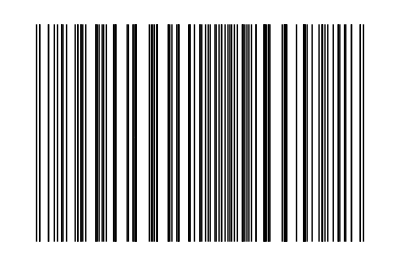

```mathematica
Show[img,Table[Graphics@Line[{{xslab[[i]],-1},{xslab[[i]],1}}],{i,Length@xslab}]]
```

```mathematica
time[[3]]=AbsoluteTiming[cellsInSlabs=<|Table[i->{},{i,Length@setxslab}]|>;][[1]]
```

0.0000555

```mathematica
time[[4]]=AbsoluteTiming[rangeTable=Table[xRange[cells[[i]]],{i,1,ncells}];][[1]]
```

0.0004117

```mathematica
time[[5]]=AbsoluteTiming[cellsRange=Table[{Position[setxslab,x_/;Abs[x-rangeTable[[i]][[1]]]<10^-10][[1,1]],Position[setxslab,x_/;Abs[x-rangeTable[[i]][[2]]]<10^-10][[1,1]]-1},{i,ncells}];][[1]]
```

0.0726481

```mathematica
time[[6]]=AbsoluteTiming[For[i=1,i<=ncells,++i,
For[j=cellsRange[[i,1]],j<=cellsRange[[i,2]],++j,AppendTo[cellsInSlabs[j],i]]]][[1]]
```

0.00315

```mathematica
Ψ[i_]:=SortBy[cellsInSlabs[i],Min[MyMin[cells[[#]],slabs[[i]]]]&]
```

```mathematica
time[[7]]=AbsoluteTiming[cellsInSlabs=Association[Table[i->Ψ[i],{i,Length@slabs}]];][[1]]
```

0.0863437

```mathematica
time[[8]]=AbsoluteTiming[slabInds=Table[search[setxslab,testdata[[i,1]]],{i,Length@testdata}];][[1]]
```

0.238432

```mathematica
φ[i_]:=Table[MyMin[cells[[cellsInSlabs[slabInds[[i]]][[j]]]],slabs[[slabInds[[i]]]]],{j,Length@cellsInSlabs[slabInds[[i]]]}]
```

```mathematica
time[[9]]=AbsoluteTiming[ally=Table[φ[i],{i, Length@testdata}];][[1]]
```

7.48751

```mathematica
time[[10]]=AbsoluteTiming[minYs=Table[Table[Min[ally[[i,j]]],{j,Length@ally[[i]]}],{i,Length@testdata}];][[1]]
```

0.15585

```mathematica
time[[11]]=AbsoluteTiming[cellInds=Table[search[minYs[[i]],testdata[[i,2]]],{i,Length@testdata}];][[1]]
```

0.192821

```mathematica
time[[12]]=AbsoluteTiming[y1=Table[Min[{ally[[i,cellInds[[i]],1]],ally[[i,cellInds[[i]],3]]}],{i,Length@testdata}];][[1]]
```

0.161243

```mathematica
time[[13]]=AbsoluteTiming[y2=Table[Min[{ally[[i,cellInds[[i]],2]],ally[[i,cellInds[[i]],4]]}],{i,Length@testdata}];][[1]]
```

0.163905

```mathematica
time[[14]]=AbsoluteTiming[y=Table[(y2[[i]]-y1[[i]])/(slabs[[slabInds[[i]],2]]-slabs[[slabInds[[i]],1]])*(testdata[[i,1]]-slabs[[slabInds[[i]],1]])+y1[[i]],{i,Length@testdata}];][[1]]
```

0.0422196

```mathematica
time[[15]]=AbsoluteTiming[res=Table[If[testdata[[i,2]]>y[[i]],cellsInSlabs[slabInds[[i]]][[cellInds[[i]]]],cellsInSlabs[slabInds[[i]]][[cellInds[[i]]-1]]],{i,Length@testdata}];][[1]]
```

0.0166528

```mathematica
Total[time]
```

{8.6215}

```mathematica
Export["test2.txt",{Length@res}~Join~res]
```

test2.txt